# lorentzian4 cutoff

## fix smear and σ; calculate <g|ρ|g> for ε ϵ [5Ω,15Ω]; compare for different values of ε

## parameters

```mathematica
α=1;
Ω=1;
```

```mathematica
numSteps=10;
εMin=5Ω;εMax=15 Ω; εStepSize=Abs[εMin-εMax]/numSteps;
εValues=Table[ε,{ε,εMin,εMax,εStepSize}];
```

## smearing function

```mathematica
σ0=10^-4/Ω;
σ=σ0;
σNorm=σ/σ0;
```

```mathematica
f[x_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

## switching function

```mathematica
chiT1[t_]:=A/2*(1+Cos[r/π(t+c)])
chiT2[t_]:=A
chiT3[t_]:=A/2*(1+Cos[r/π(t-c)])
```

## k integrand

### the first interval

```mathematica
tpInt1[t_?NumericQ,k_?NumericQ]:=tpInt1[t,k]=NIntegrate[chiT1[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-c-r,t}]
```

```mathematica
tInt1[k_?NumericQ]:=tInt1[k]=α*NIntegrate[chiT1[t] tpInt1[t,k],
{t,-c-r,-c}]
```

### the second interval

```mathematica
tpInt2[t_,k_]:=Integrate[chiT2[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-c,t}]
```

```mathematica
tInt2[k_]:=α*Integrate[chiT2[t] tpInt2[t,k],
{t,-c,c}]
```

### the third interval

```mathematica
tpInt3[t_?NumericQ,k_?NumericQ]:=tpInt3[t,k]=NIntegrate[chiT3[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,c,t}]
```

```mathematica
tInt3[k_?NumericQ]:=tInt3[k]=α*NIntegrate[chiT3[t] tpInt3[t,k],
{t,c,c+r}]
```

this integrand with the transition from Abs[k] → k taken into account (i.e. can now properly integrate from 0 to ∞ with proper factor of 2)

```mathematica
kIntegrand[k_]:=-1/π*k*ftil[k]^2*(tInt1[k]+tInt2[k]+tInt3[k])
```

## cutoff function

```mathematica
lor4Cutoff[k_,ε_]:=ε^4/(Abs[k]^4+ε^4);
```

## <g|ρ|g>

```mathematica
c=2;r=0.2;A=(2*c+r+(4π)/r*Sin[r^2/(4π)])^-1;
```

```mathematica
pLor4=Table[α+λ^2*NIntegrate[lor4Cutoff[k,ε]*kIntegrand[k],{k,0,∞}],{ε,εMin,εMax,εStepSize}]
```

{1-0.121479 λ^2,1-0.129027 λ^2,1-0.136089 λ^2,1-0.142811 λ^2,1-0.149236 λ^2,1-0.155364 λ^2,1-0.161187 λ^2,1-0.166692 λ^2,1-0.171872 λ^2,1-0.176723 λ^2,1-0.181248 λ^2}

## plot

```mathematica
λ=0.1;Ω=.;
```

```mathematica
dataLor4=Transpose[{εValues,pLor4}];
```

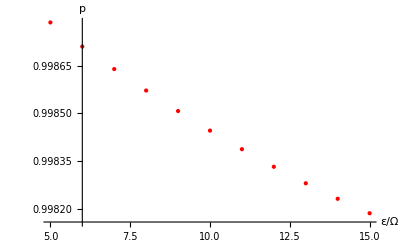

```mathematica
ListPlot[{dataLor4},
AxesLabel->{ε/Ω,p},
PlotStyle->{Red},
PlotLabel->Style["",FontSize->16]]
```

## save the data!!

```mathematica
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pLor4vEpsilon.csv",dataLor4];
```